```mathematica
p1[x_]:= a1*x^3+b1*x^2+c1*x+d1
p2[x_] := a2*x^3+b2*x^2+c2*x+d2
p3[x_] := 0.5
p4[x_] := a4*x^3+b4*x^2+c4*x+d4
p5[x_] :=0.075*x-0.55
p6[x_] := a6*x^3+b6*x^2+c6*x+d6
p7[x_]:=1.25
p8[x_] := a8*x^3+b8*x^2+c8*x+d8
```

```mathematica
Solve[{p1[0]==.75,p1[1/2]==1.25, p1[1]==0.5,p1'[1/2]==0},{a1,b1,c1,d1}]
```

{{a1→-1.,b1→-1.,c1→1.75,d1→0.75}}

```mathematica
Solve[{p2[0.5] ==p1[0.5],p2[1.5]==p3[1.5],p2'[0.5]==p1'[0.5],p2'[1.5]==p3'[1.5]},{a2,b2,c2,d2}]
```

{{a2→-1.+1. a1+1.5 b1+2. c1+2. d1,b2→3.-3.375 a1-5. b1-6.5 c1-6. d1,c2→-2.25+3.375 a1+4.875 b1+6. c1+4.5 d1,d2→0.5-0.84375 a1-1.125 b1-1.125 c1}}

```mathematica
Solve[{p4[13.5] ==p3[13.5],p4[14.5]==p5[14.5],p4'[13.5]==p3'[13.5],p4'[14.5]==p5'[14.5]},{a4,b4,c4,d4}]
```

{{a4→2.63678×10^-16,b4→0.0375,c4→-1.0125,d4→7.33437}}

```mathematica
Solve[{p6[23.5] ==p5[23.5],p6[24.5]==p7[24.5],p6'[23.5]==p5'[23.5],p6'[24.5]==p7'[24.5]},{a6,b6,c6,d6}]
```

{{a6→-1.80411×10^-16,b6→-0.0375,c6→1.8375,d6→-21.2594}}

```mathematica
Solve[{p8[33] ==p7[33],p8[33.5]==0.75,p8'[33]==p7'[33], p8'[33.5] == -10},{a8,b8,c8,d8}]
```

{{a8→-32.,b8→3182.,c8→-105468.,d8→1.16523×10^6}}

```mathematica
p1[x_] := -1*x^3-1*x^2 + 1.75*x + 0.75
p2[x_] :=1.5*x^3+-4.5*x^2 + 3.375*x + 0.5
p4[x_]:=0.0375*x^2-1.0125*x+7.334374999999278
p6[x_]:= -0.0375*x^2+1.8375*x -21.259374999997508
```

```mathematica
spline[x_]:= Piecewise[{{p1[x], 0≤ x< 0.5},{p2[x], 0.5≤ x<1.5},{p3[x],1.5≤ x< 13.5},{p4[x],13.5≤x<14.5},{p5[x],14.5≤x<23.5},{p6[x],23.5≤x<24.5},{p7[x],24.5≤ x≤33}}]
```

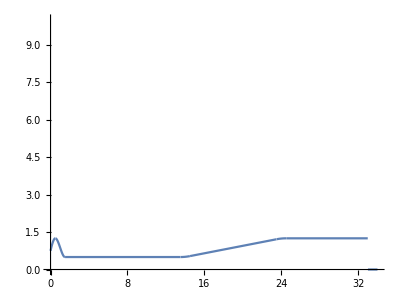

```mathematica
Plot[spline[x],{x,0,34}, AspectRatio->.75, PlotRange->{0,10}]
```